Asociaciones

Las asociaciones son un tipo de generalización de las listas, donde cada elemento tiene una clave, además de un valor. Counts es una función típica que produce una asociación.

Counts produce una asociación que informa cuántas veces aparece cada elemento diferente:

```mathematica
Counts[{a,a,b,c,a,a,b,c,c,a,a}]
```

<|a→6,b→2,c→3|>

Se obtiene el valor asociado con una clave usando [...].

Encuentre el valor asociado con c en la asociación:

```mathematica
<|a->6,b->2,c->3|>[c]
```

3

Las operaciones para trabajar con listas también funcionan con las asociaciones, aunque se aplican solamente a los valores y no a las claves.

Aquí se suma 500 a cada valor de la asociación:

```mathematica
<|a->6,b->2,c->3|>+500
```

<|a→506,b→502,c→503|>

/@ aplica una función a cada uno de los valores en la asociación:

```mathematica
f/@<|a->6,b->2,c->3|>
```

<|a→f[6],b→f[2],c→f[3]|>

Total da el total de los valores:

```mathematica
Total[<|a->6,b->2,c->3|>]
```

11

Sort opera sobre los valores:

```mathematica
Sort[<|a->6,b->2,c->3|>]
```

<|b→2,c→3,a→6|>

KeySort opera sobre las claves:

```mathematica
KeySort[<|c->1,b->2,a->4|>]
```

<|a→4,b→2,c→1|>

Las funciones Keys y Values extraen las claves y los valores en una asociación.

Obtenga la lista de las claves en la asociación:

```mathematica
Keys[<|a->6,b->2,c->3|>]
```

{a,b,c}

Obtenga la lista de los valores en la asociación:

```mathematica
Values[<|a->6,b->2,c->3|>]
```

{6,2,3}

Normal convierte una asociación en una lista normal de reglas. Association produce una asociación a partir de una lista de reglas.

```mathematica
Normal[<|a->6,b->2,c->3|>]
```

{a→6,b→2,c→3}

```mathematica
Association[{a->6,b->2,c->3}]
```

<|a→6,b→2,c→3|>

LetterCounts cuenta las veces que aparecen las letras en una cadena de caracteres.

Cuente cuántas veces aparece cada letra en el artículo de Wikipedia sobre “computers”:

```mathematica
LetterCounts[WikipediaData["computers"]]
```

<|e→4833,t→3528,a→3207,o→3059,r→2907,i→2818,n→2747,s→2475,c→1800,l→1673,m→1494,h→1473,u→1357,d→1329,p→1153,g→818,f→766,y→594,b→545,w→456,v→391,k→174,T→150,A→110,I→101,C→84,M→82,x→77,S→68,P→64,q→58,U→55,B→45,H→43,E→42,R→41,L→41,z→38,O→38,D→37,W→30,N→29,F→28,j→25,G→23,J→17,K→14,V→10,Z→8,Q→4,ū→4,ī→4,ö→2,ā→2,Y→1,X→1,é→1,â→1|>

KeyTake elige los elementos de una asociación que aparezcan en la lista de claves que se especifique. Aquí se toman los elementos cuyas claves sean letras en el alfabeto inglés (en minúsculas).

Tome solo aquellos elementos de la asociación cuyas claves aparezcan como letras del alfabeto inglés:

```mathematica
KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[ ]]
```

<|a→3207,b→545,c→1800,d→1329,e→4833,f→766,g→818,h→1473,i→2818,j→25,k→174,l→1673,m→1494,n→2747,o→3059,p→1153,q→58,r→2907,s→2475,t→3528,u→1357,v→391,w→456,x→77,y→594,z→38|>

BarChart grafica los valores en una asociación. Si se especifica ChartLabels→Automatic, se usarán las claves como etiquetas.

Haga un diagrama de barras con el número de veces que aparece cada letra; la más común es la “e” :

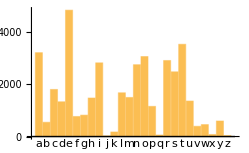

```mathematica
BarChart[KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[ ]],ChartLabels->Automatic]
```

He aquí una forma directa de aplicar una función pura a una asociación:

Aplique una función pura a una asociación:

```mathematica
f[#["apples"],#["oranges"]]&[<|"apples"->10,"oranges"->12,"pears"->4|>]
```

f[10,12]

Es muy frecuente que las claves sean cadenas de caracteres, y Wolfram Language se vale de esto en una forma especial cuando se usan funciones puras: simplemente se usa #clave cuando se haga referencia a un elemento cuya clave sea "clave".

Use la notación simplificada para los elementos de la asociación cuyas claves sean cadenas de caracteres:

```mathematica
f[#apples,#oranges]&[<|"apples"->10,"oranges"->12,"pears"->4|>]
```

f[10,12]

Un ejemplo más realista sería aplicar una función pura que extraiga el valor de “e” del conteo de las letras, y lo divida por el total. La N da el resultado en forma decimal.

Calcule la fracción de las letras que sean “e” en el artículo “computers”:

```mathematica
#e/Total[#]& @LetterCounts[WikipediaData["computers"]]//N
```

0.11795

Vocabulario

<|clave_1→value_1,clave_2→value_2, ...|> |   | una asociación
Association[reglas] |   | convierte una lista de reglas en una asociación
assoc[clave] |   | extrae un elemento de una asociación
Keys[assoc] |   | lista de las claves de una asociación
Values[assoc] |   | lista de valores en una asociación
Normal[assoc] |   | convierte una asociación en una lista de reglas
KeySort[assoc] |   | ordena una asociación según sus claves
KeyTake[assoc,claves] |   | toma elementos con claves dadas
#clave |   | ranura de función para un elemento con clave
 “clave”
Counts[lista] |   | una asociación con los conteos de los elementos
 que sean diferentes
LetterCounts[cadena] |   | una asociación con los conteos de las letras
que sean diferentes

"6 Exercises Available" | "Get Started »"

Forme la lista, ordenada, del número de veces que aparece cada uno de los dígitos del 0 al 9 en 3^100. »

| Expected output: |  
  | {7,9,9,5,1,5,4,7,1} |

Construya un diagrama de barras, con etiquetas, del número de veces que aparece cada uno de los dígitos del 0 al 9 en 2^1000. »

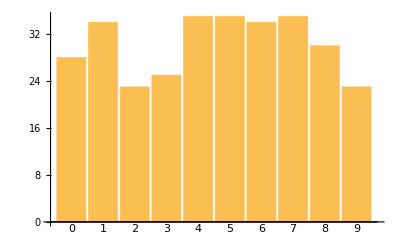
| Expected output: |  
  | -Graphics- |

Produzca un diagrama de barras, con etiquetas, del número de veces que aparece cada una de las letras iniciales en las palabras obtenidas de WordList[ ]. »

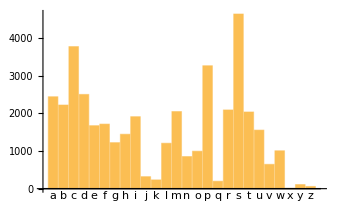
| Expected output: |  
  | -Graphics- |

Construya una asociación que muestre las 5 letras iniciales más frecuentes en las palabras obtenidas de WordList[ ], junto con sus conteos. »

| Expected output: |  
  | <|"s"→4642,"c"→3776,"p"→3267,"d"→2504,"a"→2443|> |

Encuentre la razón numérica del número de veces que ocurren la “q” y la “u” en el artículo de Wikipedia sobre “computers”. »

| Sample expected output: |  
  | 0.0426784 |

Encuentre las 10 palabras más frecuentes en ExampleData[{"Text","AliceInWonderland"}]. »

| Expected output: |  
  | {"the","and","a","to","she","of","was","Alice","in","it"} |

Preguntas y respuestas

¿Por qué se llaman así las “asociaciones”?

Porque asocian valores con claves. Otras denominaciones para lo mismo son: arreglos asociativos, diccionarios, hashmaps, structs, mapas clave-valor y listas indexadas simbólicamente.

¿Cómo se escribe en el teclado una asociación?

Se comienza con <| (< seguido de |), y luego se escribe -> para cada →. Alternativamente, se puede usar Association[a->1,b->2].

En una asociación, ¿puede haber varios elementos con la misma clave?

No. En una asociación las claves son únicas.

¿Qué pasa si se pide una clave que no esté en una asociación?

Por lo general, se obtiene Missing[...]. Sin embargo, si se usa Lookup para buscar la clave, puede especificarse la respuesta que se quiere ver cuando la clave no existe.

¿Cómo se pueden realizar operaciones con las claves de una asociación?

Se usa KeyMap, o funciones tales como KeySelect y KeyDrop. AssociationMap crea una asociación mapeando una función sobre un conjunto de claves.

¿Cómo pueden combinarse varias asociaciones en una sola?

Se usa Merge. Se requiere dar una función que indique qué hacer cuando aparezca la misma clave en múltiples asociaciones.

¿Puede usarse [[...]] para extraer una parte de una asociación, del mismo modo que se extraen partes de una lista?

Sí, si se dice explícitamente assoc[[Key[clave]]]. Por ejemplo, assoc[[2]] extrae el segundo elemento de assoc, cualquiera que sea la clave que tenga. assoc[[clave]] es un caso especial que funciona de igual manera que assoc[clave].

¿Qué sucede en el caso de funciones puras cuando las claves en una asociación no son cadenas de caracteres?

En ese caso, no puede usarse #key; tiene que usarse explícitamente #[key].

Notas técnicas

La mayoría de las funciones operan efectivamente con asociaciones como si estuvieran operando con las listas de sus valores. Generalmente, las funciones que se enhebran con listas hacen lo mismo con asociaciones.

Las asociaciones son como tablas en una base de datos relacional. JoinAcross hace lo análogo de juntar bases de datos.

Para explorar más

Guía para asociaciones en Wolfram Language »